```mathematica
D[Cos[x]Cosh[y],x]
```

-Cosh[y] Sin[x]

```mathematica
Flatten[Table[{x,y},{x,{π/2,π}},{y,Range[0.5,3,0.5]}],1]
```

{{π/2,0.5},{π/2,1.},{π/2,1.5},{π/2,2.},{π/2,2.5},{π/2,3.},{π,0.5},{π,1.},{π,1.5},{π,2.},{π,2.5},{π,3.}}

```mathematica
Table[{x,y},{x,{1,2}},{y,{1}}]
```

{{{1,1}},{{2,1}}}

```mathematica
Union[{{0,1},{0,-1},{π,1},{π,-1}},Flatten[Table[{x,y},{x,{π/2,π}},{y,Range[0.5,3,0.5]}],1]]
```

{{0,-1},{0,1},{π/2,0.5},{π/2,1.},{π/2,1.5},{π/2,2.},{π/2,2.5},{π/2,3.},{π,-1},{π,0.5},{π,1},{π,1.},{π,1.5},{π,2.},{π,2.5},{π,3.}}

```mathematica
Complement[Range[-3,3,0.5],{0.}]
```

{-3.,-2.5,-2.,-1.5,-1.,-0.5,0.5,1.,1.5,2.,2.5,3.}

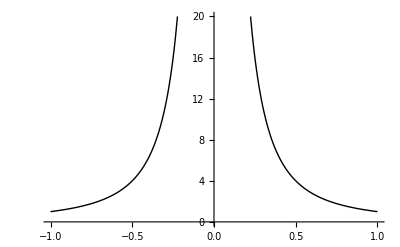

```mathematica
Plot[1/x^2,{x,-1,1},PlotRange->{0,20}]
```

```mathematica
Plot3D[
(√(x^2+y^2))^-1,
{x,-1,1},
{y,-1,1}]
```

-Graphics3D-

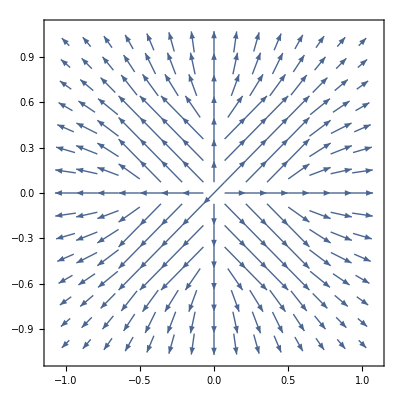

```mathematica
VectorPlot[{
Max[-1,Min[(1/(√(x^2+y^2))^2)Normalize[{x,y}]⟦1⟧,1]],
Max[-1,Min[(1/(√(x^2+y^2))^2)Normalize[{x,y}]⟦2⟧,1]]
},{x,-1,1},{y,-1,1}]
```